```mathematica
ClearAll["Global`*"];
```

```mathematica
r=1.5;
K=2;
A=2;
H=0.8;
B=1.0;
h1=1;
h2=2;
e1=0.09;
e2=0.8;
S1=1;
S2=2;
M=0.1;
d=0.1;
α=0.2;
v=5;
μ=0.001;

Tf = 10000;
eqs={
Res'[t]==r*Res[t]*(1-Res[t]/K)-((A*Res[t])/(1+H*A*Res[t]))*Con[t]-((q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*Res[t])/(1+H*A*Res[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t])+(e2*S2*α*Con[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
q'[t]==v*((Res[t]*S1*(e1+Con[t]*S2*(e1*h2-e2*h1)))/(1+S1*h1*Res[t]*q[t]+S2*h2*Con[t])^2)+μ/q[t]-μ/(1-q[t]),
Res[0]==1, Con[0]==1, Pred[0]==1,q[0]==0.5};

s = NDSolve[eqs, {Res,Con, Pred, q},{t,0,Tf}]
```

{{Res→InterpolatingFunction[{{0., 10000.}}, <>],Con→InterpolatingFunction[{{0., 10000.}}, <>],Pred→InterpolatingFunction[{{0., 10000.}}, <>],q→InterpolatingFunction[{{0., 10000.}}, <>]}}

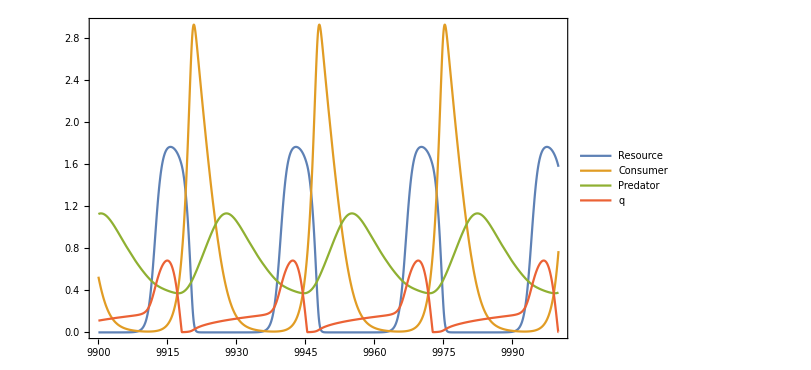

```mathematica
Plot[
Evaluate[{Res[t], Con[t],Pred[t],q[t]}/.s],
{t,9900,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource", "Consumer", "Predator", "q"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

```mathematica
Table[{Res[t]/.s, Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 0.01}]//Mean
```

{{1.109},{0.279498},{0.684313}}

```mathematica
{{0.07428218884992649},{0.7515303579720101},{0.}}
```

{{0.0742822},{0.75153},{0.}}

```mathematica
ClearAll["Global`*"];
r=1.5;
K=2;
A=2;
H=0.5;
B=1.0;
h1=1;
h2=2;
e1=0.09;
e2=0.8;
S1=1;
S2=2;
M=0.1;
d=0.1;
v=5;
μ=0.001;

Tf = 10000;
eqs={
Res'[t]==r*Res[t]*(1-Res[t]/K)-((A*Res[t])/(1+H*A*Res[t]))*Con[t]-((q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*Res[t])/(1+H*A*Res[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t])+(e2*S2*α*Con[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
q'[t]==v*((Res[t]*S1*(e1+Con[t]*S2*(e1*h2-e2*h1)))/(1+S1*h1*Res[t]*q[t]+S2*h2*Con[t])^2)+μ/q[t]-μ/(1-q[t]),
Res[0]==1, Con[0]==1, Pred[0]==1,q[0]==0.5};

Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res,Con, Pred, q},{t,0,Tf}];
Sow[
{i, Table[{Res[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 9000, 10000, 0.01}]//Mean}
];
,{i, 0.2, 1, 0.1}
]
][[2,1]]
```

{{0.2,{{0.61394},{0.571688},{1.7627}}},{0.3,{{0.840195},{0.372342},{1.92277}}},{0.4,{{0.841711},{0.312778},{1.62206}}},{0.5,{{0.923741},{0.273437},{1.51879}}},{0.6,{{0.965357},{0.281206},{1.18219}}},{0.7,{{1.00527},{0.287689},{0.992159}}},{0.8,{{1.05859},{0.281154},{0.855728}}},{0.9,{{1.0813},{0.282166},{0.762124}}},{1.,{{1.109},{0.279498},{0.684313}}}}

{{1.90947},{0.0693712},{0.106819}}

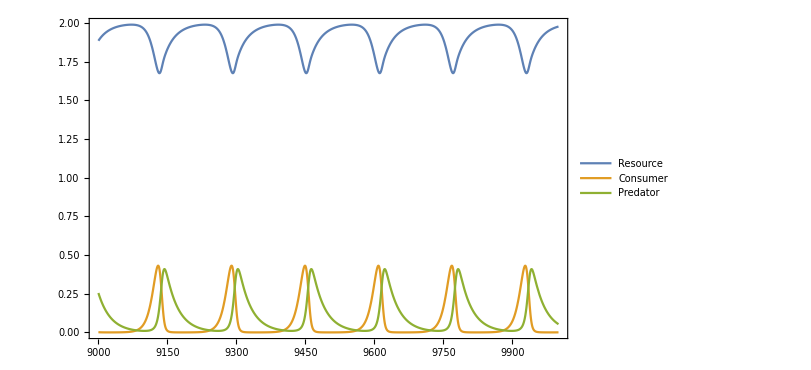

```mathematica
ClearAll["Global`*"];
r=1.5;
K=2;
A=2;
H=0;
B=0.2;
S1=1;
h1=0.8;
e1=0.1;
S2=2;
h2=1.2;
e2=0.8;
M=0.1;
d=0.1;

α=0.1;
z=(0.7*(1-α))/(0.1+(1-α))+0.3;

Tf = 10000;
eqs={
Res'[t]==r*Res[t]*(1-Res[t]/K)-((A*Res[t])/(1+H*A*Res[t]))*Con[t]-((S1*z*Res[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*Res[t])/(1+H*A*Res[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*z*Res[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t])+(e2*S2*α*Con[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res[0]==1, Con[0]==1, Pred[0]==1};
s = NDSolve[eqs, {Res,Con, Pred, q},{t,0,Tf}];
Table[{Res[t]/.s, Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 0.01}]//Mean
Plot[
Evaluate[{Res[t], Con[t],Pred[t]}/.s],
{t,9000,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

```mathematica
ClearAll["Global`*"];
r=1.5;
K=2;
A=1;
H=0.8;
B=0.2;
S1=1;
h1=0.8;
e1=0.1;
S2=2;
h2=1;
e2=0.8;
M=0.1;
d=0.1;

z=1;

Tf = 10000;
eqs={
Res'[t]==r*Res[t]*(1-Res[t]/K)-((A*Res[t])/(1+H*A*Res[t]))*Con[t]-((S1*z*Res[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*Res[t])/(1+H*A*Res[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*z*Res[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t])+(e2*S2*α*Con[t])/(1+S1*z*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 9000, 10000, 0.01}]//Mean}
];
,{i, 0.1, 0.99, 0.05}
]
][[2,1]]
```

{{0.1,{{1.45791},{0.506013},{0.392253}}},{0.15,{{1.62986},{0.320966},{0.331926}}},{0.2,{{1.71928},{0.234337},{0.276272}}},{0.25,{{1.77397},{0.184344},{0.234355}}},{0.3,{{1.81085},{0.151864},{0.202779}}},{0.35,{{1.8374},{0.129086},{0.178422}}},{0.4,{{1.85742},{0.112236},{0.159154}}},{0.45,{{1.87307},{0.0992247},{0.143583}}},{0.5,{{1.88551},{0.0891762},{0.130706}}},{0.55,{{1.89554},{0.0812682},{0.119983}}},{0.6,{{1.90461},{0.0724465},{0.111614}}},{0.65,{{1.90945},{0.0717348},{0.103113}}},{0.7,{{1.91669},{0.064674},{0.0955521}}},{0.75,{{1.91532},{0.0681401},{0.093633}}},{0.8,{{1.93299},{0.0528158},{0.074374}}},{0.85,{{1.92786},{0.0544338},{0.0810251}}},{0.9,{{1.92471},{0.0616287},{0.078507}}},{0.95,{{1.92985},{0.0685029},{0.0613424}}}}

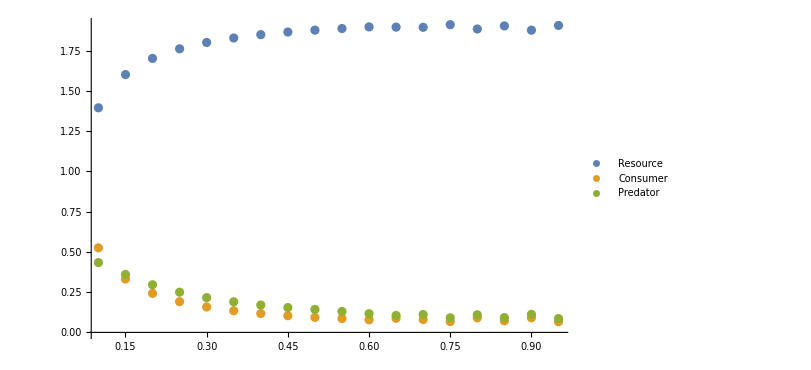

```mathematica
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]}, {n,1, 18}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[2]][[1]]}, {n,1, 18}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]}, {n,1, 18}]},
PlotLegends->{"Resource", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
```

{{0.826697},{0.24741},{1.44918},{1.4041}}

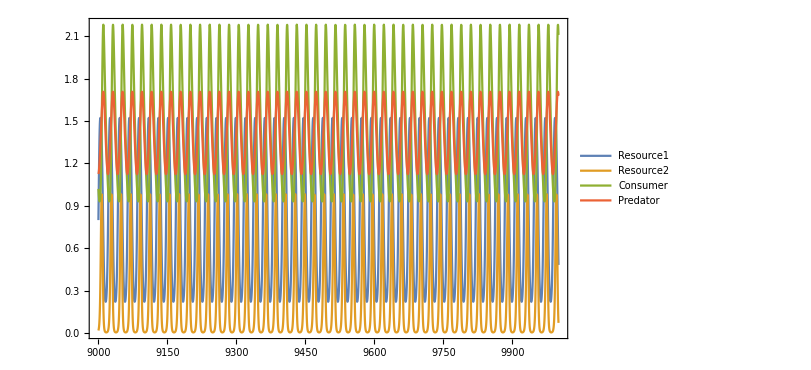

```mathematica
ClearAll["Global`*"];
r1=2;
K1=3;
r2=2;
K2=3;
A=1.5;
H=0.4;
B=0.30;
S1=1.5;
h1=0.5;
e1=0.15;
S2=0.03;
h2=0.9;
e2=0.5;
M=0.1;
d=0.1;

α=1.0;
p=0.1;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};
s = NDSolve[eqs, {Res1,Res2, Con, Pred, q},{t,0,Tf}];
Table[{Res1[t]/.s, Res2[t]/.s, Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 0.01}]//Mean
Plot[
Evaluate[{Res1[t], Res2[t], Con[t],Pred[t]}/.s],
{t,9000,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource1", "Resource2", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

```mathematica
ClearAll["Global`*"];
r1=2;
K1=3;
r2=2;
K2=3;
A=1.5;
H=0.4;
B=0.3;
S1=1.5;
h1=0.5;
e1=0.15;
S2=0.1;
h2=0.2;
e2=0.5;
M=0.1;
d=0.1;

p=0.1;

Tf = 10000;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*Pred[t],
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 9000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.05}
]
][[2,1]];
```

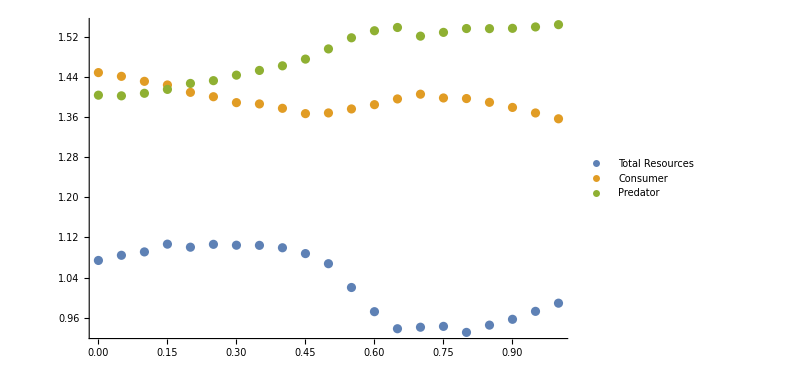

```mathematica
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]}, {n,1, 21}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 21}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
```